```mathematica
de = v*t - b*t^2/2 + (v-b*t)^2/(2*p)
do = vo^2/(2*p)
```

-(b t^2)/2+t v+(-b t+v)^2/(2 p)

vo^2/(2 p)

```mathematica
result = Simplify[Solve[de== do+g, b]]
```

{{b→(p t+2 v-√(8 g p+p^2 t^2-4 p t v+4 vo^2))/(2 t)},{b→(p t+2 v+√(8 g p+p^2 t^2-4 p t v+4 vo^2))/(2 t)}}

```mathematica
vals = {vo->27.16,v->31.23,g->99.25-50.0-4.0,p->20,t->0.75}
```

{vo→27.16,v→31.23,g→45.25,p→20,t→0.75}

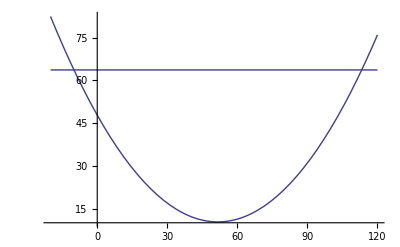

```mathematica
Plot[{de,do+g}/.vals,{b,-20,120}]
```